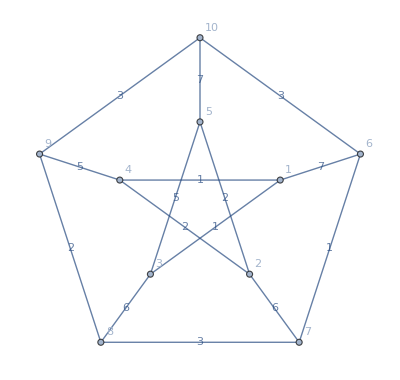

```mathematica
graph=PetersenGraph[VertexLabels->Automatic,EdgeWeight->Thread[EdgeList[PetersenGraph[]]->RandomInteger[{1,7},EdgeCount[PetersenGraph[]]]],EdgeLabels->"EdgeWeight"]
```

```mathematica
LinearOptimization[WeightedAdjacencyMatrix[graph]x,{},{x∈Matrices[{VertexCount[PetersenGraph[]],VertexCount[PetersenGraph[]]},Integers]}]
```

```mathematica
WeightedAdjacencyMatrix[graph]//Grid
```

0 | 0 | 1 | 1 | 0 | 7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 2 | 0 | 6 | 0 | 0 | 0
1 | 0 | 0 | 0 | 5 | 0 | 0 | 6 | 0 | 0
1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0
0 | 2 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 7
7 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 3
0 | 6 | 0 | 0 | 0 | 1 | 0 | 3 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 3 | 0 | 2 | 0
0 | 0 | 0 | 5 | 0 | 0 | 0 | 2 | 0 | 3
0 | 0 | 0 | 0 | 7 | 3 | 0 | 0 | 3 | 0

```mathematica
Extract[WeightedAdjacencyMatrix[graph],{{Complement[Range[10],{2,5,7}],{2,5,7}}}]
```

{SparseArray[…]}

```mathematica
Grid/@Extract[WeightedAdjacencyMatrix[graph],{{Complement[Range[10],{2,5,7}],{2,5,7}}}]
```

{0 | 0 | 0
0 | 5 | 0
2 | 0 | 0
0 | 0 | 1
0 | 0 | 3
0 | 0 | 0
0 | 7 | 0}

```mathematica
Extract[WeightedAdjacencyMatrix[graph],{{Complement[Range[10],{2,5,7}],{2,5,7}}}]\[VectorGreaterEqual]Extract[AdjacencyMatrix[graph],{{Complement[Range[10],{2,5,7}],{2,5,7}}}]
```

True

```mathematica
Grid/@Transpose[Extract[WeightedAdjacencyMatrix[graph],{{Complement[Range[10],{2,5,7}],{2,5,7}}}]]
```

{0 | 0 | 0,0 | 5 | 0,2 | 0 | 0,0 | 0 | 1,0 | 0 | 3,0 | 0 | 0,0 | 7 | 0}

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

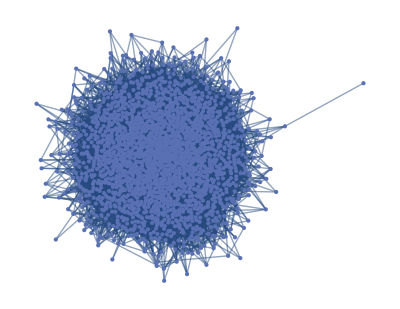

```mathematica
bigWeightedGraph=RandomWeightedMixedGraph[{2000,10000},0,RandomReal[{1,7}]&]
```

```mathematica
First@RepeatedTiming[AnnotationValue[bigWeightedGraph,EdgeWeight]]
```

1.61×10^-6

Therefore AnnotationValue is fast and works well for large graphs. we can use it as an alternative to WeightedAdjacencyMatrix for edge weights.

```mathematica
AnnotationValue[graph,EdgeWeight]
```

{1,1,7,2,2,6,5,6,5,7,1,3,3,2,3}

```mathematica
EdgeList[bigWeightedGraph,_<->1]
```

{1<->565,1<->923,1<->1245,1<->1253,1<->1393,1<->1628,1<->1829,1<->1835,1<->1948,1<->1995}

```mathematica
RepeatedTiming@EdgeList[bigWeightedGraph,_<->1]
```

{0.0000274061,{1<->565,1<->923,1<->1245,1<->1253,1<->1393,1<->1628,1<->1829,1<->1835,1<->1948,1<->1995}}

```mathematica
RepeatedTiming@EdgeList[bigWeightedGraph,_<->32|32<->_]
```

{0.00399861,{10<->32,32<->59,32<->77,32<->132,32<->210,32<->470,32<->476,32<->847,32<->1200,32<->1265,32<->1450,32<->1510,32<->1793,32<->1952}}

EdgeList is also fast enough to test:

```mathematica
LinearOptimization[AnnotationValue[graph,EdgeWeight].x,{},{x∈Vectors[EdgeCount[graph],]}]
```

```mathematica
Array[Indexed[x,{##}]&,EdgeCount[graph]]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15}

```mathematica
Array[Indexed[x,{##}]&,EdgeCount[graph]][[{2,5,7}]]
```

{x2,x5,x7}

```mathematica
Extract[Array[Indexed[x,{##}]&,EdgeCount[graph]],{{2},{5},{7}}]
```

{x2,x5,x7}

```mathematica
RepeatedTiming@Extract[Array[Indexed[x,{##}]&,10000],{{2},{5},{7}}]
```

{0.0111499,{x2,x5,x7}}

```mathematica
RepeatedTiming@Array[Indexed[x,{##}]&,10000][[{2,5,7}]]
```

{0.0108022,{x2,x5,x7}}

```mathematica
RepeatedTiming@Extract[Array[Indexed[x,{##}]&,100000],{{2},{5},{7}}]
```

{0.0990862,{x2,x5,x7}}

```mathematica
RepeatedTiming@Array[Indexed[x,{##}]&,100000][[{2,5,7}]]
```

{0.0999084,{x2,x5,x7}}

```mathematica
Needs["PeterBurbery`UndirectedGraphs`"]
```

```mathematica
PacletFind["*Peter*"]
```

{PacletObject[…],PacletObject[…],PacletObject[…]}

```mathematica
PacletInstall[ResourceObject["PeterBurbery/UndirectedGraphs"]]
```

PacletObject[…]

```mathematica
OddNodes[graph]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Round[9,2]
```

8

```mathematica
EdgeCount[graph]
```

15

```mathematica
If[EvenQ[EdgeCount[graph]],EdgeCount[graph]-1,EdgeCount[graph]]
```

15

```mathematica
If[EvenQ[16],16-1,16]
```

15

```mathematica
Subsets[OddNodes[graph],{1,If[EvenQ[EdgeCount[graph]],EdgeCount[graph]-1,EdgeCount[graph]],2}]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,2,10},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,3,10},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,4,10},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{1,5,10},{1,6,7},{1,6,8},{1,6,9},{1,6,10},{1,7,8},{1,7,9},{1,7,10},{1,8,9},{1,8,10},{1,9,10},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,3,9},{2,3,10},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,4,9},{2,4,10},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{2,5,10},{2,6,7},{2,6,8},{2,6,9},{2,6,10},{2,7,8},{2,7,9},{2,7,10},{2,8,9},{2,8,10},{2,9,10},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,4,9},{3,4,10},{3,5,6},{3,5,7},{3,5,8},{3,5,9},{3,5,10},{3,6,7},{3,6,8},{3,6,9},{3,6,10},{3,7,8},{3,7,9},{3,7,10},{3,8,9},{3,8,10},{3,9,10},{4,5,6},{4,5,7},{4,5,8},{4,5,9},{4,5,10},{4,6,7},{4,6,8},{4,6,9},{4,6,10},{4,7,8},{4,7,9},{4,7,10},{4,8,9},{4,8,10},{4,9,10},{5,6,7},{5,6,8},{5,6,9},{5,6,10},{5,7,8},{5,7,9},{5,7,10},{5,8,9},{5,8,10},{5,9,10},{6,7,8},{6,7,9},{6,7,10},{6,8,9},{6,8,10},{6,9,10},{7,8,9},{7,8,10},{7,9,10},{8,9,10},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,7},{1,2,3,4,8},{1,2,3,4,9},{1,2,3,4,10},{1,2,3,5,6},{1,2,3,5,7},{1,2,3,5,8},{1,2,3,5,9},{1,2,3,5,10},{1,2,3,6,7},{1,2,3,6,8},{1,2,3,6,9},{1,2,3,6,10},{1,2,3,7,8},{1,2,3,7,9},{1,2,3,7,10},{1,2,3,8,9},{1,2,3,8,10},{1,2,3,9,10},{1,2,4,5,6},{1,2,4,5,7},{1,2,4,5,8},{1,2,4,5,9},{1,2,4,5,10},{1,2,4,6,7},{1,2,4,6,8},{1,2,4,6,9},{1,2,4,6,10},{1,2,4,7,8},{1,2,4,7,9},{1,2,4,7,10},{1,2,4,8,9},{1,2,4,8,10},{1,2,4,9,10},{1,2,5,6,7},{1,2,5,6,8},{1,2,5,6,9},{1,2,5,6,10},{1,2,5,7,8},{1,2,5,7,9},{1,2,5,7,10},{1,2,5,8,9},{1,2,5,8,10},{1,2,5,9,10},{1,2,6,7,8},{1,2,6,7,9},{1,2,6,7,10},{1,2,6,8,9},{1,2,6,8,10},{1,2,6,9,10},{1,2,7,8,9},{1,2,7,8,10},{1,2,7,9,10},{1,2,8,9,10},{1,3,4,5,6},{1,3,4,5,7},{1,3,4,5,8},{1,3,4,5,9},{1,3,4,5,10},{1,3,4,6,7},{1,3,4,6,8},{1,3,4,6,9},{1,3,4,6,10},{1,3,4,7,8},{1,3,4,7,9},{1,3,4,7,10},{1,3,4,8,9},{1,3,4,8,10},{1,3,4,9,10},{1,3,5,6,7},{1,3,5,6,8},{1,3,5,6,9},{1,3,5,6,10},{1,3,5,7,8},{1,3,5,7,9},{1,3,5,7,10},{1,3,5,8,9},{1,3,5,8,10},{1,3,5,9,10},{1,3,6,7,8},{1,3,6,7,9},{1,3,6,7,10},{1,3,6,8,9},{1,3,6,8,10},{1,3,6,9,10},{1,3,7,8,9},{1,3,7,8,10},{1,3,7,9,10},{1,3,8,9,10},{1,4,5,6,7},{1,4,5,6,8},{1,4,5,6,9},{1,4,5,6,10},{1,4,5,7,8},{1,4,5,7,9},{1,4,5,7,10},{1,4,5,8,9},{1,4,5,8,10},{1,4,5,9,10},{1,4,6,7,8},{1,4,6,7,9},{1,4,6,7,10},{1,4,6,8,9},{1,4,6,8,10},{1,4,6,9,10},{1,4,7,8,9},{1,4,7,8,10},{1,4,7,9,10},{1,4,8,9,10},{1,5,6,7,8},{1,5,6,7,9},{1,5,6,7,10},{1,5,6,8,9},{1,5,6,8,10},{1,5,6,9,10},{1,5,7,8,9},{1,5,7,8,10},{1,5,7,9,10},{1,5,8,9,10},{1,6,7,8,9},{1,6,7,8,10},{1,6,7,9,10},{1,6,8,9,10},{1,7,8,9,10},{2,3,4,5,6},{2,3,4,5,7},{2,3,4,5,8},{2,3,4,5,9},{2,3,4,5,10},{2,3,4,6,7},{2,3,4,6,8},{2,3,4,6,9},{2,3,4,6,10},{2,3,4,7,8},{2,3,4,7,9},{2,3,4,7,10},{2,3,4,8,9},{2,3,4,8,10},{2,3,4,9,10},{2,3,5,6,7},{2,3,5,6,8},{2,3,5,6,9},{2,3,5,6,10},{2,3,5,7,8},{2,3,5,7,9},{2,3,5,7,10},{2,3,5,8,9},{2,3,5,8,10},{2,3,5,9,10},{2,3,6,7,8},{2,3,6,7,9},{2,3,6,7,10},{2,3,6,8,9},{2,3,6,8,10},{2,3,6,9,10},{2,3,7,8,9},{2,3,7,8,10},{2,3,7,9,10},{2,3,8,9,10},{2,4,5,6,7},{2,4,5,6,8},{2,4,5,6,9},{2,4,5,6,10},{2,4,5,7,8},{2,4,5,7,9},{2,4,5,7,10},{2,4,5,8,9},{2,4,5,8,10},{2,4,5,9,10},{2,4,6,7,8},{2,4,6,7,9},{2,4,6,7,10},{2,4,6,8,9},{2,4,6,8,10},{2,4,6,9,10},{2,4,7,8,9},{2,4,7,8,10},{2,4,7,9,10},{2,4,8,9,10},{2,5,6,7,8},{2,5,6,7,9},{2,5,6,7,10},{2,5,6,8,9},{2,5,6,8,10},{2,5,6,9,10},{2,5,7,8,9},{2,5,7,8,10},{2,5,7,9,10},{2,5,8,9,10},{2,6,7,8,9},{2,6,7,8,10},{2,6,7,9,10},{2,6,8,9,10},{2,7,8,9,10},{3,4,5,6,7},{3,4,5,6,8},{3,4,5,6,9},{3,4,5,6,10},{3,4,5,7,8},{3,4,5,7,9},{3,4,5,7,10},{3,4,5,8,9},{3,4,5,8,10},{3,4,5,9,10},{3,4,6,7,8},{3,4,6,7,9},{3,4,6,7,10},{3,4,6,8,9},{3,4,6,8,10},{3,4,6,9,10},{3,4,7,8,9},{3,4,7,8,10},{3,4,7,9,10},{3,4,8,9,10},{3,5,6,7,8},{3,5,6,7,9},{3,5,6,7,10},{3,5,6,8,9},{3,5,6,8,10},{3,5,6,9,10},{3,5,7,8,9},{3,5,7,8,10},{3,5,7,9,10},{3,5,8,9,10},{3,6,7,8,9},{3,6,7,8,10},{3,6,7,9,10},{3,6,8,9,10},{3,7,8,9,10},{4,5,6,7,8},{4,5,6,7,9},{4,5,6,7,10},{4,5,6,8,9},{4,5,6,8,10},{4,5,6,9,10},{4,5,7,8,9},{4,5,7,8,10},{4,5,7,9,10},{4,5,8,9,10},{4,6,7,8,9},{4,6,7,8,10},{4,6,7,9,10},{4,6,8,9,10},{4,7,8,9,10},{5,6,7,8,9},{5,6,7,8,10},{5,6,7,9,10},{5,6,8,9,10},{5,7,8,9,10},{6,7,8,9,10},{1,2,3,4,5,6,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,6,10},{1,2,3,4,5,7,8},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,8,9},{1,2,3,4,5,8,10},{1,2,3,4,5,9,10},{1,2,3,4,6,7,8},{1,2,3,4,6,7,9},{1,2,3,4,6,7,10},{1,2,3,4,6,8,9},{1,2,3,4,6,8,10},{1,2,3,4,6,9,10},{1,2,3,4,7,8,9},{1,2,3,4,7,8,10},{1,2,3,4,7,9,10},{1,2,3,4,8,9,10},{1,2,3,5,6,7,8},{1,2,3,5,6,7,9},{1,2,3,5,6,7,10},{1,2,3,5,6,8,9},{1,2,3,5,6,8,10},{1,2,3,5,6,9,10},{1,2,3,5,7,8,9},{1,2,3,5,7,8,10},{1,2,3,5,7,9,10},{1,2,3,5,8,9,10},{1,2,3,6,7,8,9},{1,2,3,6,7,8,10},{1,2,3,6,7,9,10},{1,2,3,6,8,9,10},{1,2,3,7,8,9,10},{1,2,4,5,6,7,8},{1,2,4,5,6,7,9},{1,2,4,5,6,7,10},{1,2,4,5,6,8,9},{1,2,4,5,6,8,10},{1,2,4,5,6,9,10},{1,2,4,5,7,8,9},{1,2,4,5,7,8,10},{1,2,4,5,7,9,10},{1,2,4,5,8,9,10},{1,2,4,6,7,8,9},{1,2,4,6,7,8,10},{1,2,4,6,7,9,10},{1,2,4,6,8,9,10},{1,2,4,7,8,9,10},{1,2,5,6,7,8,9},{1,2,5,6,7,8,10},{1,2,5,6,7,9,10},{1,2,5,6,8,9,10},{1,2,5,7,8,9,10},{1,2,6,7,8,9,10},{1,3,4,5,6,7,8},{1,3,4,5,6,7,9},{1,3,4,5,6,7,10},{1,3,4,5,6,8,9},{1,3,4,5,6,8,10},{1,3,4,5,6,9,10},{1,3,4,5,7,8,9},{1,3,4,5,7,8,10},{1,3,4,5,7,9,10},{1,3,4,5,8,9,10},{1,3,4,6,7,8,9},{1,3,4,6,7,8,10},{1,3,4,6,7,9,10},{1,3,4,6,8,9,10},{1,3,4,7,8,9,10},{1,3,5,6,7,8,9},{1,3,5,6,7,8,10},{1,3,5,6,7,9,10},{1,3,5,6,8,9,10},{1,3,5,7,8,9,10},{1,3,6,7,8,9,10},{1,4,5,6,7,8,9},{1,4,5,6,7,8,10},{1,4,5,6,7,9,10},{1,4,5,6,8,9,10},{1,4,5,7,8,9,10},{1,4,6,7,8,9,10},{1,5,6,7,8,9,10},{2,3,4,5,6,7,8},{2,3,4,5,6,7,9},{2,3,4,5,6,7,10},{2,3,4,5,6,8,9},{2,3,4,5,6,8,10},{2,3,4,5,6,9,10},{2,3,4,5,7,8,9},{2,3,4,5,7,8,10},{2,3,4,5,7,9,10},{2,3,4,5,8,9,10},{2,3,4,6,7,8,9},{2,3,4,6,7,8,10},{2,3,4,6,7,9,10},{2,3,4,6,8,9,10},{2,3,4,7,8,9,10},{2,3,5,6,7,8,9},{2,3,5,6,7,8,10},{2,3,5,6,7,9,10},{2,3,5,6,8,9,10},{2,3,5,7,8,9,10},{2,3,6,7,8,9,10},{2,4,5,6,7,8,9},{2,4,5,6,7,8,10},{2,4,5,6,7,9,10},{2,4,5,6,8,9,10},{2,4,5,7,8,9,10},{2,4,6,7,8,9,10},{2,5,6,7,8,9,10},{3,4,5,6,7,8,9},{3,4,5,6,7,8,10},{3,4,5,6,7,9,10},{3,4,5,6,8,9,10},{3,4,5,7,8,9,10},{3,4,6,7,8,9,10},{3,5,6,7,8,9,10},{4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,10},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,7,8,9,10},{1,2,3,4,6,7,8,9,10},{1,2,3,5,6,7,8,9,10},{1,2,4,5,6,7,8,9,10},{1,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10}}

```mathematica
Array[Indexed[x,{##}]&,100000]&/@Subsets[OddNodes[graph],{1,If[EvenQ[EdgeCount[graph]],EdgeCount[graph]-1,EdgeCount[graph]],2}]
```

```mathematica
ResourceFunction["ResourceSubmissions"][]
```

{ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…]}

```mathematica
ResourceFunction["PacletizeResourceFunction"]["BirdSay"]
```

PacletObject[…]

```mathematica
?BirdSay
```